# Physics of Electron Microscopy Instrumentation

## Georgios Varnavides | March 2nd 2026

## Transfer Matrices & Ray Diagrams

## Motivation

The derived linear properties we extracted from the paraxial rays allow us to construct ray diagrams, which provide an intuitive, geometric picture of electron trajectories through an optical column.

A ray diagram is a geometric representation of how electron trajectories propagate through an optical system composed of lenses, drift spaces, and apertures. 
In electron microscopy, ray diagrams are commonly used to:

Visualize beam convergence and divergence

Identify crossover and image planes

Understand how apertures limit angular or spatial acceptance

Build intuition for multi-element systems such as SEM and TEM columns

Below, we will use ray diagrams to model a simple scanning electron microscope (SEM) consisting of two condenser lenses, an objective lens, and several apertures.

## Transfer Matrix Formalism

In the paraxial regime, ray propagation can be expressed using ray transfer matrices.
A ray at axial position z is represented by the vector (r
r') where r is the transverse displacement and r' is the slope.

#### Free-space propagation

Propagation over a distance d is described by

	M_prop(d)=(1 | d
0 | 1).

#### Thin lens

An ideal thin lens with focal length f is described by

	M_lens(f)=(1 | 0
-1/f | 1).

#### Apertures

Apertures play a fundamentally different role from lenses and drift spaces.
They do not transform rays; instead, they select which rays are allowed to continue.

An aperture is therefore modeled as a constraint:

If  , the ray passes through unchanged.

If  , the ray is blocked and removed from further propagation.

In ray diagrams, apertures appear as physical stops that clip the ray bundle, defining beam current and angular acceptance rather than optical power.

#### Ray propagation though a multi-component system

The ray after passing through an optical element is obtained by simple matrix multiplication:

	(r_out
r'_out)=M (r_in
r'_in)
	
For a sequence of elements, the total transfer matrix is the ordered product of the individual matrices. This makes it straightforward to assemble complex systems from simple components.
With these ingredients—transfer matrices for lenses and propagation, and constraints for apertures—we can now build and visualize a complete thin-lens SEM ray diagram.

```mathematica
transferMatrix["propagation"][d_]:={{1,d},{0,1}};
transferMatrix["lens"][f_]:={{1,0},{-1/f,1}};

applyTransferMatrix[M_,ray_]:=M.ray;

traceRaySequence[ray0_,sequence_]:=Block[
{
ray=ray0,z=0.0,traj={{0.0,ray0}}
},
Do[
Switch[
elem["type"],
"propagation",

z+=elem["dz"];
ray=applyTransferMatrix[transferMatrix["propagation"][elem["dz"]],ray];
AppendTo[traj,{z,ray}],

"lens",
ray=applyTransferMatrix[transferMatrix["lens"][elem["focal_length"]],ray];
AppendTo[traj,{z,ray}],

"aperture",
If[Abs[ray[[1]]]>elem["aperture_radius"],Return[traj]],

_,Continue[]
],
{elem,sequence}
];
traj
]
```

## Ray Tracing

We will explicitly define electro-optical components in our SEM (lenses and apertures) using their axial position and focal length / aperture radius.

```mathematica
Clear[electroOpticalComponents]
electroOpticalComponents[{f1_,f2_,f3_},{ap1_,ap2_}]:={
<|"type"->"lens","name"->"1^st condenser lens","axial_position"->0.2,"focal_length"->f1|>,
<|"type"->"aperture","name"->"spray aperture","axial_position"->0.5,"aperture_radius"->ap1|>,
<|"type"->"lens","name"->"2^nd condenser lens","axial_position"->0.7,"focal_length"->f2|>,
<|"type"->"aperture","name"->"objective aperture","axial_position"->1.2,"aperture_radius"->ap2|>,
<|"type"->"lens","name"->"objective lens","axial_position"->1.3,"focal_length"->f3|>,
<|"type"->"sample","name"->"sample","axial_position"->1.5|>
}
```

```mathematica
Dataset[exampleAlignment = electroOpticalComponents[{0.05,0.15,0.35},{0.05,0.05}]]
```

Propagation elements will then be inferred in the free-space between electro-optical components.

```mathematica
parseOpticalSequence[
components_List,
zStart_,
zEnd_
]:=Block[{sorted,zPrev,seq={}},
sorted=SortBy[components,#["axial_position"]&];

zPrev=zStart;
Do[
If[
comp["axial_position"]>zPrev,
AppendTo[
seq,
<|"type"->"propagation","dz"->comp["axial_position"]-zPrev|>
];
];
AppendTo[seq,comp];
zPrev=comp["axial_position"];
,{comp,sorted}
];

If[
zPrev<zEnd,
AppendTo[seq,<|"type"->"propagation","dz"->zEnd-zPrev|>];
];

seq
]
```

```mathematica
parsedComponents = parseOpticalSequence[exampleAlignment,0.0,1.7];
template = AssociationMap[Missing[]&,Union@@Keys[parsedComponents]];
Dataset[Join[template,#]&/@parsedComponents]
```

We can now use the parsed sequence to trace uniformly spaced rays inside the electron gun semiangle:

```mathematica
traceRaysOpticalSequence[components_List,zStart_,zEnd_,semiangle_,numRays_:128]:=Block[
{opticalSequence,rays,graphics},
opticalSequence=parseOpticalSequence[components,zStart,zEnd];
rays = Table[traceRaySequence[{0,Tan[α]},opticalSequence],{α,Subdivide[-semiangle,semiangle,numRays]}
];
rays
]
```

```mathematica
exampleRays=traceRaysOpticalSequence[exampleAlignment,0.0,1.7,0.15,128];
exampleRays[[;;5]]
```

{{{0.,{0,-0.151135}},{0.2,{-0.030227,-0.151135}},{0.2,{-0.030227,0.453406}},{0.5,{0.105795,0.453406}}},{{0.,{0,-0.148739}},{0.2,{-0.0297478,-0.148739}},{0.2,{-0.0297478,0.446216}},{0.5,{0.104117,0.446216}}},{{0.,{0,-0.146344}},{0.2,{-0.0292688,-0.146344}},{0.2,{-0.0292688,0.439032}},{0.5,{0.102441,0.439032}}},{{0.,{0,-0.143951}},{0.2,{-0.0287902,-0.143951}},{0.2,{-0.0287902,0.431853}},{0.5,{0.100766,0.431853}}},{{0.,{0,-0.141559}},{0.2,{-0.0283119,-0.141559}},{0.2,{-0.0283119,0.424678}},{0.5,{0.0990916,0.424678}}}}

## Ray Diagrams Plotting

We can plot the rays by drawing straight-line segments between each breakpoint.
By convention, we draw the rays as propagating in the negative -z direction and, naturally, in green.

```mathematica
plotRays[rays_,zStart_,zEnd_]:=ListLinePlot[
rays/. {z_,{r_,_}}:>{r,-z},
Frame->True,
PlotRange->{{-0.25,0.25},{-zStart+0.1,-zEnd-0.1}},
PlotStyle->RGBColor[0,0.5,0.0,0.5],
AspectRatio->2,
FrameTicks->None,
PlotHighlighting->None,
PlotRange->{300,600}
]
```

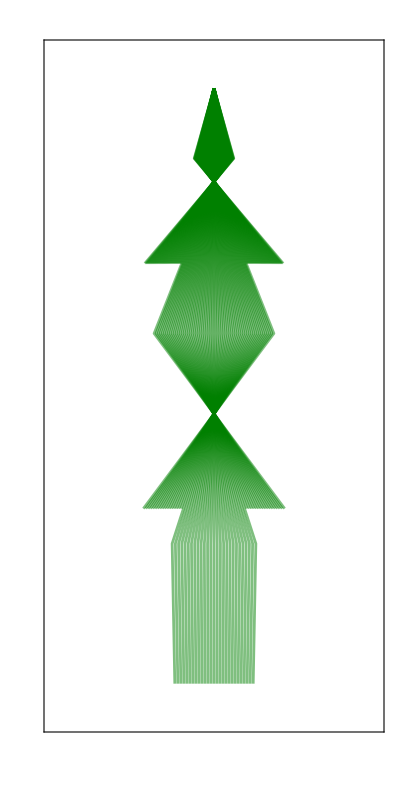

```mathematica
plotRays[exampleRays,0.0,1.7]
```

This looks correct, but hard to understand the action of the lenses / apertures like this.
Let’s add them on the ray diagram using graphic primitives.

```mathematica
Clear[componentGraphics,singleComponentGraphics]
singleComponentGraphics["sample"][z_, width_:0.1,thickness_:0.0075]:={Rectangle[{-width/2,-z-thickness},{width/2,-z+thickness}]}
singleComponentGraphics["lens"][z_,rx_:0.15,ry_:0.0125]:={Circle[{0,-z},{rx,ry}]}
singleComponentGraphics["aperture"][z_,innerRadius_,outerRadius_:0.15,thickness_:0.0075]:={
LightGray,
Rectangle[{-outerRadius,-z-thickness},{-innerRadius,-z+thickness}],
Rectangle[{innerRadius,-z-thickness},{outerRadius,-z+thickness}]
}
componentGraphics[element_]:=Switch[
element["type"],
"lens",singleComponentGraphics["lens"][element["axial_position"]],
"aperture",singleComponentGraphics["aperture"][element["axial_position"],element["aperture_radius"]],
"sample",singleComponentGraphics["sample"][element["axial_position"]],
_,Nothing
]
```

```mathematica
computeAndShowRayDiagram[components_List,zStart_,zEnd_,semiangle_,numRays_:128]:=Block[{rays,graphics},
rays = traceRaysOpticalSequence[components,zStart,zEnd,semiangle,numRays];
graphics = Graphics[componentGraphics/@components];
Show[
plotRays[rays,zStart,zEnd],
graphics
]
]
```

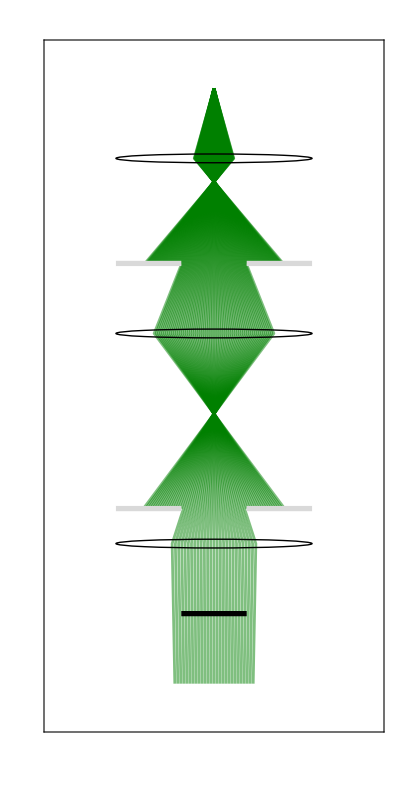

```mathematica
computeAndShowRayDiagram[exampleAlignment,0.0,1.7,0.15,128]
```

## Interactive SEM Ray Diagram

We can also make an interactive version of the ray diagram, by wrapping these functions in a Dynamic Module.
Notice we also specify the control elements at specific heights to match the electro-optical components’ axial positions.

```mathematica
DynamicModule[{f1,f2,f3,ap1,ap2},
Manipulate[
computeAndShowRayDiagram[
electroOpticalComponents[{f1,f2,f3},{ap1,ap2}],
0,1.7,
0.15
],
Column[{
Spacer[{0,62}],
Control[{{f1,0.05,StringPadRight["condenser lens 01 focal length (m)",35]},0.025,0.5,ImageSize->100}],
Spacer[{0,40 }],
Control[{{ap1,0.05,StringPadRight["spray aperture radius (m)",35]},0.025,0.2,ImageSize->100}],
Spacer[{0,20 }],
Control[{{f2,0.15,StringPadRight["condenser lens 02 focal length (m)",35]},0.025,0.5,ImageSize->100}],
Spacer[{0,83}],
Control[{{ap2,0.05,StringPadRight["objective aperture radius (m)",35]},0.025,0.2,ImageSize->100}],
Control[{{f3,0.35,StringPadRight["objective lens focal length (m)",35]},0.025,0.5,ImageSize->100}]
}
],
Paneled->False,
ControlPlacement->Right
]
]
```